-Graphics-

# 快速入门Wolfram技术

## 语法和编程

-Graphics-

## 学习目标

本节将向您介绍如何编写 Wolfram 语言代码.

### 表达式

理解 Wolfram 语言中的一切都是表达式

识别表达式的结构和构建块

从结构相似的表达中解释不同的含义

将表达式可视化为树以及引用其部分

### 结构化数据

根据项目的需要构建数据

在列表中创建项目的通用集合

将键值对存储在关联中

在数据集中呈现分层数据

### 赋值

使用两种不同的赋值形式为符号赋值

立即赋值 （Immediate assignment）

延迟赋值 （Delayed assignment）

### 函数定义

定义你自己的自定义函数

将 SetDelayed 识别为定义函数的便捷选择

使用模式来限制函数的输入

### 高级编程概念

了解 Wolfram 语言如何实现符号计算

探索函数式编程的各个方面

在列表中映射与应用函数

构造纯函数

思考解决重复运算的不同方法

## 表达式

Wolfram 语言中的一切都是符号表达式。有时表达式看起来很相似；有时它们看起来非常不同.

这是 Wolfram 语言表达式的结构：

Head[elem_1, elem_2, elem_3, …]

但是，它们可能以不同的格式出现在Wolfram笔记本中.

以下是 Wolfram 语言中的几个表达式示例：

```mathematica
DateString[]
```

```mathematica
ListPlot[{3,8,3,10,3,0,3,3,1,4}]
```

```mathematica
Histogram[]
```

```mathematica
Cases[{x,y,3,4,z,6,7},_Integer]
```

```mathematica
Solve[3x==x/7 -5,x]
```

```mathematica
StringJoin["Hello","World"]
```

```mathematica
Classify["Language","the house is blue"]
```

```mathematica
ImageEffect[-Graphics-,"EdgeStylization"]
```

```mathematica
GeoGraphics[GeoMarker[],GeoRange->Quantity[1,"Miles"]]
```

## 了解表达式

#### 看起来很相似的表达式

Head[elem_1, elem_2, elem_3, …]

在前面的示例中，您可以看到：

所有表达式都以一个以大写字母开头的单词开头.

都有方括号.

方括号中的元素使用逗号相互分隔.

有时方括号内没有元素.

#### 看起来非常不同的表达式

您还将遇到与所示模板完全不同的表达式.

但是，您可以使用 FullForm 函数来显示它们真正的底层结构：

```mathematica
a+b
```

```mathematica
FullForm[a+b]
```

```mathematica
{a,b,c,d,e}
```

```mathematica
FullForm[{a,b,c,d,e} ]
```

```mathematica
Plot[Sin[x], {x, 0, 10}]
```


```mathematica
FullForm[-Graphics-]
```

也可以用 FullForm 来查看上一张幻灯片中的部分表达式的底层结构：

```mathematica
FullForm[]
```

```mathematica
FullForm[-Graphics-]
```

```mathematica
FullForm[_Integer]
```

```mathematica
FullForm[3x==x/7 -5]
```

#### 表达式头部

开头方括号之前的表达式部分称为表达式的头部.

用 Head 来提取表达式的头部：

```mathematica
a+b/2 c
```

```mathematica
Head[a+b/2 c]
```

#### 表达式的原子元素

Wolfram 语言中的所有表达式最终都是由少数不同类型的原子元素构成的.

数字：整数、有理数、实数、复数和其他数字表示：

```mathematica
127
```

```mathematica
3/4
```

```mathematica
0.0004
```

```mathematica
3.777
```

```mathematica
5+3I
```

字符串：用双引号括起来的任何内容：

```mathematica
"String"
```

```mathematica
"123"
```

符号：不以数字开头的字符连接：

```mathematica
symbol
```

```mathematica
variable
```

```mathematica
x
```

符号是 Wolfram 语言中的基本命名对象。每个符号都有一个唯一的名称.
符号名字：

由字母、数字和其他字符的串联组成

不能以数字开头

不能以某些保留的特殊字符开头或包含某些保留的特殊字符（例如 !、@、#、%、^、+、-、_、=、&、(、)、{、}、[、] 等）

#### 复合表达式

可以组合原子表达式来构建复合表达式. 您还可以嵌套复合表达式以逐步构建更复杂的表达式。

这是一个由多个原子元素组成的复合表达式：

```mathematica
Manipulate[Histogram[RandomReal[{-1,1},a],PlotLabel->"Example of Histogram",PlotTheme->"Monochrome"],{{a,10},{10,100,1000,10000}}]
```

这是一个嵌套表达式：

```mathematica
Sin[Cos[Exp[Tan[RandomReal[]]]]]
```

## 表达式的含义

表达式的概念是 Wolfram 系统中一个至关重要的统一原则. 事实上，Wolfram 系统中的每个对象都具有相同的底层结构，这使得 Wolfram 系统能够以相对较少的基本操作覆盖如此多的领域.

这是一个简单的表达式：

f[x,y, …]

f 的含义可以解释为：

以 x 和 y 作为参数的函数：Sin[x]

以 x 和 y 作为参数的命令：Expand[(x+1)^2]

以 x 和 y 作为操作数的运算符：x+y 或 Plus[x,y]

一种以 x 和 y 为内容的对象：RGBColor[1,0,0]

以 x 和 y 作为元素的头部：{x,y,z} 或 List[x,y,z]

### 其他输入表达式的方法

在大多数情况下，表达式以标准形式出现：

```mathematica
Mean[{1,2,3}]
```

```mathematica
Sin[Cos[Exp[Tan[RandomReal[]]]]]
```

相同的表达式可以写成前缀形式：

```mathematica
Mean@{1,2,3}
```

```mathematica
Sin@Cos@Exp@Tan@RandomReal[]
```

相同的表达式也可以写成后缀形式：

```mathematica
{1,2,3}//Mean
```

```mathematica
RandomReal[]//Tan//Exp//Cos//Sin
```

### 表达式树

您可以将任何 Wolfram 语言表达式视为一棵树.

这是一个完整的表达式：

```mathematica
FullForm[x^3+(1+x)^2]
```

TreeForm 打印表达式的“树”结构：

```mathematica
TreeForm[x^3+(1+x)^2]
```

### 表达式的一部分

现在您已经可视化了由许多部分构建的表达式，您可以考虑单独或组合使用这些部分.

你可以使用 Part 函数来提取表达式的任何部分：

```mathematica
(x+y+z)//TreeForm
```

```mathematica
Part[(x+y+z),2]
```

```mathematica
(x+y+z)[[2]]
```

```mathematica
{a,b,c}//TreeForm
```

```mathematica
{a,b,c}[[3]]
```

```mathematica
(x^3+(1+x)^2)//TreeForm
```

```mathematica
(x^3+(1+x)^2)[[1,1]]
```

## 结构化数据：列表

列表（List ）是 Wolfram 语言中收集事物的一种基本方式.

列表示例：

```mathematica
{1,2,3,4,5}
```

```mathematica
{a,42,3.14,RGBColor[1, 0, 0],"hello", x^2+3 y^3,-Graphics3D-}
```

列表可以用作：

物品容器

一个集合

向量或矩阵

变量/表达式列表：

```mathematica
{a,b,c,d,e}
```

颜色的集合（注意：Wolfram 语言具有预定义的颜色符号）：

```mathematica
{Red, Blue, Green}
```

数字列表：

```mathematica
{1,3.4,-5,7.8}
```

表示整数矩阵的嵌套列表：

```mathematica
{{1,2},{3,4}}
```

Part 函数可用于从列表中提取元素：

```mathematica
Part[{a,b,c,d,e},2]
```

更常用的是快捷符号 [[ ]]：

```mathematica
myList = {a,b,c,d,e}
```

```mathematica
myList[[2]]
```

```mathematica
myList[[-1]]
```

```mathematica
myList[[3;;5]]
```

```mathematica
myList[[4;;]]
```

```mathematica
myList[[{1,4}]]
```

## 结构化数据：关联

关联（ Association）是包含键值对的字典数据结构. 它是符号索引列表、关联数组、字典、哈希图等的概括. 关联将标记数据表示为键→值对.

假设您需要记录班级学生的测验分数. 你可以有一个学生列表和他们的测验分数列表.

学生列表：

```mathematica
students = {"Alice","Bob","Charlie","Dan"};
```

测验分数列表：

```mathematica
quizScores = {90,20,70,75};
```

现在，如果您需要查找 Charlie 的分数，您必须记住 Charlie 是列表中的第三个学生，因此他的分数是 quizScores 列表中的第三项.

从 quizScores 列表中获取第三项：

```mathematica
quizScores[[3]]
```

如何将每个分数与相应的学生相关联？

创建一个关联来存储每个学生的测验分数：

```mathematica
studentQuizScores =<|"Alice"->90,"Bob"->20,"Charlie"->70,"Dan"->75|>
```

获取键“Charlie”对应的值：

```mathematica
studentQuizScores["Charlie"]
```

### 构建关联

您可以使用特殊语法来创建关联.

从头开始创建关联：

```mathematica
Association[a->1,b->2]
```

```mathematica
<|a->1,b->2|>
```

关联可以将任何 Wolfram 语言表达式作为键或值，但键必须是唯一的：

```mathematica
assoc=<|a->1,{2,3}->2,4->3,"cat"->-Graphics-|>
```

```mathematica
assoc["cat"]
```

```mathematica
assoc=<|a->1,{2,3}->2,4->3,"cat"->-Graphics-,"cat"->5|>
```

许多 Wolfram 语言函数以关联的形式显示它们的输出.

统计一个元素在列表中出现的次数：

```mathematica
Counts[{a,b,c,a}]
```

统计每个字母在计算机上的维基百科文章中出现的次数：

```mathematica
LetterCounts[ToLowerCase[WikipediaData["computers"]]]
```

可以使用  Keys 或 Values:快速列出关联的所有键和值：

```mathematica
assoc
```

```mathematica
Keys[assoc]
```

```mathematica
Values[assoc]
```

## 结构化数据：数据集

数据集（Dataset）用于表示分层结构化数据.

这是一个由关联的关联形成的数据集的简单示例：

```mathematica
data=Dataset[<|"a"-><|"x"->1,"y"->2,"z"->3|>,"b"-><|"x"->5,"y"->10,"z"->7|>|>]
```

可以按如下方式访问各个行和列中的元素：

```mathematica
data["b","z"]
```

```mathematica
data["b"]
```

```mathematica
data[All,"z"]
```

您可以在任何地方提取部分，也可以将函数应用于该部分的所有零件：

```mathematica
data[All,PieChart]
```

```mathematica
data[Total,"x"]
```

# 快速回顾

## 赋值

可以使用  Set(=) 和 SetDelayed (:=)将值赋给符号.  赋值的规则是将左侧 (LHS) 赋值为右侧 (RHS).

### 立即赋值

这是立即赋值的形式：

LHS = RHS

运算右侧并将结果立即赋为左侧的值：

```mathematica
a=3
```

```mathematica
b=a^2
```

### 延迟赋值

这是延迟赋值的形式:

LHS := RHS

右侧会保持未经计算的初始形式.每当左侧符号出现在表达式中时,左侧才会被右侧替换，并且右侧的值每次都重新计算：

```mathematica
a=3;
```

```mathematica
b=a^2;
```

```mathematica
c:= a^2;
```

```mathematica
b
```

```mathematica
c
```

```mathematica
a=2;
```

```mathematica
b
```

```mathematica
c
```

```mathematica
?b
```

```mathematica
?c
```

## 函数定义

函数的概念在 Wolfram 语言中比在传统数学或计算机科学中更为宽泛.

例如：

f[anything]

被认为是一个函数，无论其被运行为确定的内容还是保持符号形式.

使用 Wolfram 语言中内置的函数已经可以完成很多工作. 但有时您需要定义自己的函数，而 Wolfram 语言有一种非常灵活的方式来做到这一点.

函数通常定义为：

LHS := RHS

左侧通常是函数的名称，以及它期望的输入的形式.  右侧RHS 定义了描述如何使用函数的输入参数来计算函数返回的结果的规则.

带有单个下划线字符的单个空格Blank (_)  表示可以代表任何 Wolfram 语言表达式的模式. 可以通过在空格前面加上代表名称的字符来给该模式命名.

### 示例 1

定义一个将输入翻倍并加以 20 的函数：

```mathematica
fun[x_]:= 2 x + 20
```

使用该函数获取输入值为 21 的结果：

```mathematica
fun[21]
```

使用该函数获取输入值为 12 的结果：

```mathematica
fun[12]
```

### 示例 2

定义一个接受两个输入参数并将第一个输入参数的平方与第二个输入参数的三倍相加的函数：

```mathematica
fun2[x_,z_]:= x^2 + 3 z
```

在该函数中带入两个输入值：

```mathematica
fun2[2,3]
```

### 示例 3

定义一个函数，该函数接受一段文本和一种颜色作为参数，然后识别文本的语言并在地图上以指定颜色突出显示该语言使用者最多的国家：

```mathematica
languageCountry[word_,color_]:= GeoListPlot[LanguageIdentify[word]["LargestCountry"],PlotStyle->color]
```

在不同的输入上尝试该函数：

```mathematica
languageCountry["la maison est bleue",Blue] (*French*)
```

```mathematica
languageCountry["будинок синій",Red] (*Ukranian*)
```

### 示例 4

这是 Wolfie 的图像：

您可以更改 Wolfie 的颜色：

```mathematica
ColorReplace[-Graphics-,White-> LightGreen]
```

定义一个允许用户指定颜色作为输入的函数：

```mathematica
colorWolfie[color_]:= ColorReplace[-Graphics-,White-> color]
```

现在该函数可用于制作不同颜色的图像：

```mathematica
colorWolfie[Pink]
```

```mathematica
colorWolfie[Brown]
```

## 为什么使用延迟赋值？

在定义自己的函数时，您可能不希望立即运算右侧并赋值给左侧. 您可能只希望在赋值期间记录定义，并在调用函数时进行实时运算. 这将使 延迟赋值(:=) 在定义此类函数时成为一个方便的选择。

定义一个根据提供的输入为 Wolfie 着色并将背景从红色更改为随机颜色的函数：

```mathematica
colorWolfieWithRandomBackground[color_]:= ColorReplace[-Graphics-,{White-> color,Red-> RandomColor[]}]
```

创建一个浅绿色的 Wolfie：

```mathematica
colorWolfieWithRandomBackground[LightGreen]
```

创建一个浅蓝色 Wolfie：

```mathematica
colorWolfieWithRandomBackground[LightBlue]
```

如果没有使用延迟赋值(:=)来定义函数，它的行为将不会像预期的那样.

使用立即赋值 (=) 而不是延迟赋值 (:=) 来定义一个函数：

```mathematica
colorWolfieWithRandomBackground[color_]:= ColorReplace[-Graphics-,{White-> color,Red-> RandomColor[]}];
```

```mathematica
yetAnotherColorWolfie[color_] =  ColorReplace[-Graphics-,{White-> color,Red-> RandomColor[]}];
```

为符号color分配一个值并重新计算前面的函数定义：

```mathematica
color = Gray
```

再次使用该函数：

```mathematica
yetAnotherColorWolfie[LightGreen]
```

```mathematica
yetAnotherColorWolfie[LightBlue]
```

这两个函数的定义不同：

```mathematica
?colorWolfieWithRandomBackground
```

```mathematica
?yetAnotherColorWolfie
```

## 用模式定义函数输入

尝试创建一个紫红色的 Wolfie：

```mathematica
colorWolfie[color_]:= ColorReplace[-Graphics-,White-> color];
```

```mathematica
colorWolfie[Fuchsia]
```

```mathematica
colorWolfie[Red]
```

### 使输入更具体

受限模式可用于函数定义中，以限定函数将处理的输入类型.

通过以下形式来使更加具体（输入_类型）：

```mathematica
x_Integer
```

可以使用 PatternTest  和计算结果为真或假的判定函数来使模式更具体：

```mathematica
x_?IntegerQ[x]
```

Wolfram 语言有许多用于测试表达式的判定函数，它们的名称通常以 Q 结尾. 例如: IntegerQ, StringQ, PossibleZeroQ 等. 更多的判定函数可以在测试表达式中找到.

也可以使用条件来使模式更加具体，输入必须必须通过条件测试才能并满足表达式并进行运算：(模式/;条件).

```mathematica
x_/;x>0&& IntegerQ[x]
```

### 定义一个以针对不同类型的输入以不同方式工作的函数

清除 colorWolfie 函数的定义：

```mathematica
Clear[colorWolfie]
```

重新定义 colorWolfie 函数，使其仅在提供 RGBColor 作为输入时尝试替换图像中的白色：

```mathematica
colorWolfie[color_RGBColor] :=ColorReplace[-Graphics-,White-> color]
```

现在用紫红色试试看：

```mathematica
colorWolfie[Fuchsia]
```

在有效的 RGBColor 上尝试该函数：

```mathematica
colorWolfie[RGBColor[1,0,1]]
```

为任何非 RGBColor 输入的colorWolfie添加另一个定义：

```mathematica
colorWolfie[anything_]:= "The input is not recognized as an RGBColor"
```

再次用紫红色试试看：

```mathematica
colorWolfie[Fuchsia]
```

用其他输入进行尝试：

```mathematica
colorWolfie["Red"]
```

```mathematica
colorWolfie[Red]
```

## 内置函数

虽然您可以定义和使用您选择的任何函数，但 Wolfram 语言中内置了 6000 多个函数. 这些函数很容易识别：

函数的名字以大写字母开头，他们在方括号内接受输入.

函数名称通常是直观的完整英文单词或标准数学缩写，便于在文档中心搜索：

```mathematica
Range[10]
```

```mathematica
RandomInteger[100]
```

```mathematica
RandomInteger[100,10]
```

```mathematica
Max[44,22,7,88,94,51,12,42,34,6]
```

```mathematica
Solve[2x-7==0,x]
```

```mathematica
Integrate[Sin[x],x]
```

```mathematica
Plot[Sin[x]/x,{x,-Pi,Pi}]
```

```mathematica
ImageIdentify[-Graphics-]
```

```mathematica
WordTranslation["pancake","Canadian"]
```

# 快速回顾

## 符号计算

Wolfram 语言是符号性的.

这里，x 只是一个符号：

```mathematica
x
```

符号变量可能是“未定义的”，用来代表自己：

```mathematica
Mean[{x,2 x,5 x}]
```

其他东西也用符号进行表示：

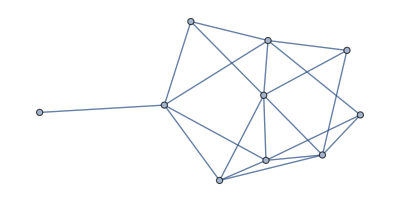
```mathematica
{42,RGBColor[1, 0, 0],-Graphics-,LinguisticAssistant,-Graphics-}
```

这是一个应用于符号x的称为 f 的符号函数：

```mathematica
f[x]
```

它可以应用于其他输入：

```mathematica
f[42]
```

```mathematica
f[RGBColor[1, 0, 0]]
```

函数 Framed 会在它所应用的任何对象周围显示一个框架：

```mathematica
Framed[x]
```

```mathematica
Framed[-Graphics-]
```

```mathematica
Framed[-Graphics-]
```

```mathematica
Framed[LinguisticAssistant]
```

把整个列表框起来：

```mathematica
Framed[{42,RGBColor[1, 0, 0],-Graphics-,LinguisticAssistant,-Graphics-}]
```

这个函数在每个对象周围放置一个框架：

```mathematica
Map[Framed,{42,RGBColor[1, 0, 0],-Graphics-,LinguisticAssistant,-Graphics-}]
```

## 函数式编程

凭借其符号特征，Wolfram 语言支持基于广义变换的函数式编程的扩展形式.

表示函数操作的 Wolfram 语言函数不仅可以对普通数据进行操作，还可以对函数本身进行操作.

### 将函数应用于列表

Wolfram 语言提供了一套优雅的函数式编程结构，用于将函数并行应用于列表中的许多元素.

使用 Map 为列表中的每个项目提供一个框架：

```mathematica
Map[Framed,{-Graphics-,LinguisticAssistant,-Graphics-}]
```

改用 Map  的简写符号：

```mathematica
Framed /@ {-Graphics-,LinguisticAssistant,-Graphics-}
```

在 Wolfram 语言中，许多函数是自动“可列表循环的”，因此它们总是应用于列表中的每个元素：

```mathematica
Log[E]
```

```mathematica
Log[{a,b,c}]
```

```mathematica
WordStem["running"]
```

```mathematica
WordStem[{"run","running","test","testing"}]
```

使用 Apply  替换表达式的头部（将其从 List 更改为  Plus）：

```mathematica
FullForm[{a,b,c}]
```

```mathematica
Apply[newhead,{a,b,c}]
```

```mathematica
{{a,b,c},{x,y,z}}//TreeForm
```

```mathematica
Apply[Plus,{{a,b,c},{x,y,z}},{1}]
```

```mathematica
{{a,b,c},{x,y,z}}//TreeForm
```

```mathematica
{a+b+c,x+y+z}//TreeForm
```

使用 Apply 的简写符号：

```mathematica
newhead@@{a,b,c}
```

```mathematica
Plus@@@{{a,b,c},{x,y,z}}
```

## 函数式编程

### 纯函数

Wolfram 语言允许使用以 & 结尾的纯函数. 函数的参数用# 表示（多个参数可以用#1、#2 等表示）:

这是一个纯函数：

```mathematica
#^2+ 3# -2&
```

它可以用于单个输入：

```mathematica
#^2+ 3# -2&[42]
```

它可以用于列表输入：

```mathematica
#^2+ 3# -2& /@ {23,42,56}
```

以下“纯函数”在每个对象后面放置一个随机背景颜色：

```mathematica
Framed[#,Background->RandomColor[]]&/@{-Graphics-,LinguisticAssistant,-Graphics-}
```

这个纯函数接受多个参数：

```mathematica
#1+2 #2+#3^3 &[a,b,c]
```

## 重复运算

在重复执行任何计算时，Wolfram 语言提供了许多不同的选项.

Map 可用于对列表中的每个元素执行相同的操作：

```mathematica
Alphabet[]
```

```mathematica
Map[Framed[#,Background-> RandomColor[]]&,Alphabet[]]
```

```mathematica
Framed[#,Background-> RandomColor[]]&/@Alphabet[]
```

Table 不仅可以用于构建向量和数组，还可以在构建迭代器时将函数应用于迭代器：

```mathematica
Table[i,{i,10}]
```

```mathematica
Table[Total[IntegerDigits[i^2]],{i,10}]
```

```mathematica
Alphabet[]
```

```mathematica
{c,Alphabet[]}
```

```mathematica
Table[Framed[c,Background-> RandomColor[]],{c,Alphabet[]}]
```

Nest 函数族可用于连续将符号函数 f 应用于 x：

```mathematica
NestList[f,x,10]
```

如果将 Framed 应用于函数，则生成嵌套框：

```mathematica
NestList[Framed,x,10]
```

使用纯函数在每边框内放置随机背景颜色：

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

通过将 “BorderingContries” 属性嵌套两次，创建一个与瑞士及其邻国接壤的国家的图表：

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","Switzerland"],2,VertexLabels->Automatic]
```

将该概念推广到具有两个参数的函数，您可以重复应用该函数，但从列表的连续元素中获取第二个参数：

```mathematica
FoldList[f,x,{a,b,c}]
```

更传统的For, While 和 Do  循环结构也可用于 Wolfram 语言.

## 参考文献

表达式

列表

关联

结构化数据集的计算

定义变量和函数

功能和程序

功能操作